```mathematica
SetDirectory["C:\\Users\\Georg\\Desktop\\figs"];
<<"CustomTicks.m"
```

```mathematica
ϵ=.
μ=.
Ω=.
u=.
i0=Integrate[(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
i1=Integrate[u(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
i2=Integrate[u^2(-μ/(-1+u (ϵ μ+λ)-Ω)+(1+ϵ)μ/(1+u (ϵ μ+λ)-Ω)),{u,0,1},Assumptions->μ∈Reals&&ϵ∈Reals&&Ω∉Reals&&λ>0]
```

(μ ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)]))/(λ+ϵ μ)

(μ (ϵ λ+ϵ^2 μ-(1+ϵ) (-1+Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω]+Ω Log[1+Ω]-Log[1-λ-ϵ μ+Ω]-Ω Log[1-λ-ϵ μ+Ω]))/(λ+ϵ μ)^2

(μ ((λ+ϵ μ) (-4+ϵ (-2+λ+ϵ μ+2 Ω))+4 (1+Ω^2) ArcTanh[Ω]-2 (ϵ (-1+Ω)^2-2 Ω) Log[1-Ω]-2 Log[1-λ-ϵ μ+Ω]+2 ((1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 Ω Log[1+Ω]-Ω (2+Ω) Log[1-λ-ϵ μ+Ω])))/(2 (λ+ϵ μ)^3)

```mathematica
h=.
FullSimplify[(h-i1)^2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals&&λ>0]
```

((λ+ϵ μ) (h λ+(-1+h) ϵ μ)-μ (2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω])+μ (1+Ω) Log[1-λ-ϵ μ+Ω])^2/(λ+ϵ μ)^4

```mathematica
FullSimplify[-i0 i2,Assumptions->μ∈Reals&&ϵ>0&&Ω∉Reals&&h∈Reals&&λ>0]
```

-1/(2 (λ+ϵ μ)^4)μ^2 ((λ+ϵ μ) (-4+ϵ (-2+λ+ϵ μ+2 Ω))+4 (1+Ω^2) ArcTanh[Ω]-2 (ϵ (-1+Ω)^2-2 Ω) Log[1-Ω]-2 Log[1-λ-ϵ μ+Ω]+2 ((1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 Ω Log[1+Ω]-Ω (2+Ω) Log[1-λ-ϵ μ+Ω])) ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)])

```mathematica
d[h_,ϵ_,μ_,λ_,Ω_]:=((λ+ϵ μ) (h λ+(-1+h) ϵ μ)-μ (2 Ω ArcTanh[Ω]+(1+ϵ-ϵ Ω) Log[1-Ω]+(1+ϵ) (-1+Ω) Log[1+λ+ϵ μ-Ω]+Log[1+Ω])+μ (1+Ω) Log[1-λ-ϵ μ+Ω])^2/(λ+ϵ μ)^4-1/(2 (λ+ϵ μ)^4)μ^2 ((λ+ϵ μ) (-4+ϵ (-2+λ+ϵ μ+2 Ω))+4 (1+Ω^2) ArcTanh[Ω]-2 (ϵ (-1+Ω)^2-2 Ω) Log[1-Ω]-2 Log[1-λ-ϵ μ+Ω]+2 ((1+ϵ) (-1+Ω)^2 Log[1+λ+ϵ μ-Ω]+2 Ω Log[1+Ω]-Ω (2+Ω) Log[1-λ-ϵ μ+Ω])) ((1+ϵ) Log[(1+λ+ϵ μ-Ω)/(1-Ω)]-Log[(1-λ-ϵ μ+Ω)/(1+Ω)])
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

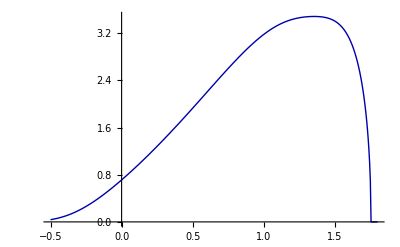

```mathematica
λ=3.;
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[1,0.5,m,λ,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
t=Table[{a,k[10^a]},{a,-0.5,1.8,0.005}];
t01=t;
f=ListLinePlot[t,PlotStyle->{Darker[Blue],Thick}]
```

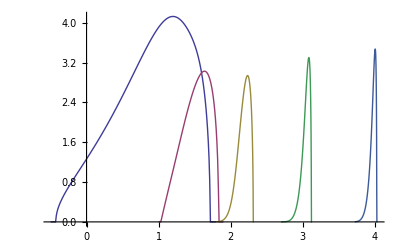

```mathematica
ListLinePlot[{t0,t1,t2,t3,t4}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

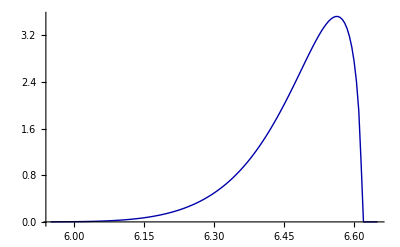

```mathematica
λ=10.^6;
Ω0=1.+0.2I;
k[μ_]:=Module[{m=μ,Ω},Ω0=Last[Last[FindRoot[d[-1,0.5,m,λ,Ω]==0,{Ω,Ω0+0.01I}]]];Abs[Im[Ω0]]]
t=Table[{a,k[10^a]},{a,6.65,5.95,-0.005}];
s6=t;
f=ListLinePlot[t,PlotStyle->{Darker[Blue],Thick}]
```

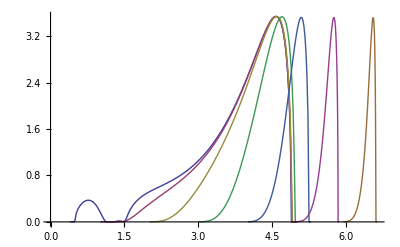

```mathematica
ListLinePlot[{s0,s1,s2,s3,s4,s5,s6}]
```

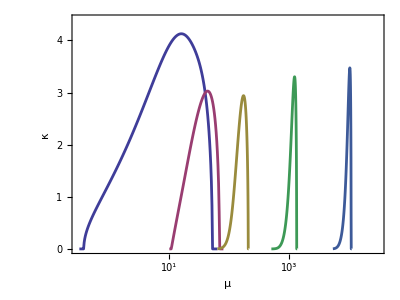

mat1.eps

```mathematica
plot1=ListLinePlot[{t0,t1,t2,t3,t4},PlotRange->{{Log[10,0.3],Log[10,30000]},{0,4.4}},AspectRatio->3/4,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{AbsoluteThickness[2]},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["μ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,6,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
Export["mat1.eps",plot1]
```

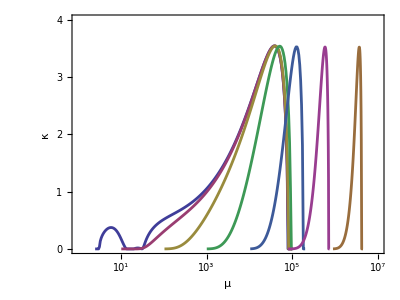

mat2.eps

```mathematica
plot2=ListLinePlot[{s0,s1,s2,s3,s4,s5,s6},PlotRange->{{Log[10,1],7},{0,4}},AspectRatio->3/4,
ImageSize->{400,400},ImagePadding->{{80,20},{80,20}},
PlotStyle->{AbsoluteThickness[2]},
BaseStyle->{FontFamily->"Helvetica",14},Frame->True,Axes->False,
FrameStyle->AbsoluteThickness[0.7],FrameLabel->{Style["μ",14],Style["κ",14]},
FrameTicks->{LogTicks[-1,7,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[-1,7,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,5,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}]
Export["mat2.eps",plot2]
```